```mathematica
Rhs2D:=Block[{},
phi2d={1-xi-eta,xi,eta};
xel=Sum[coords[[i]]phi2d[[i]],{i,3}];
gradx=Grad[xel,{xi,eta}][[1;;2]];
detjac=Det[gradx];
fmat=Integrate[phi2d detjac 100,{xi,0,1},{eta,0,1-xi}];
forcel=force[[3;;-1;;3]]//Flatten;
{fmat-forcel,fmat}
]
```

```mathematica
StiffEl[]:=Block[{},
phi3d={1-xi-eta-zeta,xi,eta,zeta};
xel=Sum[coords[[i]]phi3d[[i]],{i,4}];
gradx=Grad[xel,{xi,eta,zeta}];
detjac=Det[gradx];
gradxi=Transpose[Inverse[gradx]];
gradphixi=Grad[phi3d,{xi,eta,zeta}];
gradphix=Table[gradxi.gradphixi[[i]],{i,4}];
solx=sol[[1;;-1;;3,1]];
soly=sol[[2;;-1;;3,1]];
solz=sol[[3;;-1;;3,1]];
gradsolz=Sum[solz[[i]]gradphix[[i]],{i,4}];
BMat=Table[0,{6},{12}];
BMat[[1,1;;12;;3]]=gradphix[[1;;4,1]];
BMat[[2,2;;12;;3]]=gradphix[[1;;4,2]];
BMat[[3,3;;12;;3]]=gradphix[[1;;4,3]];
BMat[[4,1;;12;;3]]=gradphix[[1;;4,2]];
BMat[[4,2;;12;;3]]=gradphix[[1;;4,1]];
BMat[[5,1;;12;;3]]=gradphix[[1;;4,3]];
BMat[[5,3;;12;;3]]=gradphix[[1;;4,1]];
BMat[[6,2;;12;;3]]=gradphix[[1;;4,3]];
BMat[[6,3;;12;;3]]=gradphix[[1;;4,2]];
BMat.Flatten[sol];
Clear[El,nu,DMat];
DMat=Table[0,{6},{6}];
DMat[[1;;3,1;;3]]=El/(1+nu)(1-2nu){{(1-nu),nu,nu},{nu,1-nu,nu},{nu,nu,1-nu}};
DMat[[4;;6,4;;6]]=El/(1+nu)(1-2nu)(1-2nu)/2DiagonalMatrix[{1,1,1}];
El=100;
nu=0;
DMat.BMat.Flatten[sol];
stiffmat=detjac Transpose[BMat].DMat.BMat Integrate[1,{xi,0,1},{eta,0,1-xi},{zeta,0,1-xi-eta}];
{stiff,stiffmat-stiff}
]
```

{{9.6205,10.9701,11.474},{-14.832,3.11601,-0.513857},{14.8398,-3.10705,-19.4956},{-9.62835,-10.979,8.53546}}

{{0},{0},{0.0499938},{0},{0},{0},{0},{0},{0},{0},{0},{0.049953}}

{0.,0.,1.}

(9.6205 | 0 | 0 | -14.832 | 0 | 0 | 14.8398 | 0 | 0 | -9.62835 | 0 | 0
0 | 10.9701 | 0 | 0 | 3.11601 | 0 | 0 | -3.10705 | 0 | 0 | -10.979 | 0
0 | 0 | 11.474 | 0 | 0 | -0.513857 | 0 | 0 | -19.4956 | 0 | 0 | 8.53546
10.9701 | 9.6205 | 0 | 3.11601 | -14.832 | 0 | -3.10705 | 14.8398 | 0 | -10.979 | -9.62835 | 0
11.474 | 0 | 9.6205 | -0.513857 | 0 | -14.832 | -19.4956 | 0 | 14.8398 | 8.53546 | 0 | -9.62835
0 | 11.474 | 10.9701 | 0 | -0.513857 | 3.11601 | 0 | -19.4956 | -3.10705 | 0 | 8.53546 | -10.979)

{0.,0.,1.,0.,0.,0.}

```mathematica
sumres=0;
ic = 1;
coords=
{ 
{ 0.45000000000000001, 0, 0 },
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.38442083654932441, -0.037862147671478032, 0 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
stiff=
{ 
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 } };
force=
{ 
{ 0 },
{ 0 },
{ -0.090497621732262779 },
{ 0 },
{ 0 },
{ -0.090497621732262779 },
{ 0 },
{ 0 },
{ -0.090497621732262779 } };
residual=
{ 
{ 0 },
{ 0 },
{ 0.090497621732262779 },
{ 0 },
{ 0 },
{ 0.090497621732262779 },
{ 0 },
{ 0 },
{ 0.090497621732262779 } };
Rhs2D[]
sumres+=residual[[ic*3+3,1]]
```

{{0.,0.,0.},{-0.0904976,-0.0904976,-0.0904976}}[]

0.0904976

```mathematica
ic = 0;
coords=
{ 
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.41574578963007902, -0.17220754456429049, 0 },
{ 0.34846518400510601, -0.10309591846884369, 0 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
stiff=
{ 
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 } };
force=
{ 
{ 0 },
{ 0 },
{ -0.12415670134755218 },
{ 0 },
{ 0 },
{ -0.12415670134755218 },
{ 0 },
{ 0 },
{ -0.12415670134755219 } };
residual=
{ 
{ 0 },
{ 0 },
{ 0.12415670134755218 },
{ 0 },
{ 0 },
{ 0.12415670134755218 },
{ 0 },
{ 0 },
{ 0.12415670134755219 } };
sumres+=residual[[ic*3+3,1]]
ic = 0;
coords=
{ 
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.34846518400510601, -0.10309591846884369, 0 },
{ 0.38442083654932441, -0.037862147671478032, 0 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
stiff=
{ 
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 },
{ 0, 0, 0, 0, 0, 0, 
0, 0, 0 } };
force=
{ 
{ 0 },
{ 0 },
{ -0.091818932332315459 },
{ 0 },
{ 0 },
{ -0.091818932332315459 },
{ 0 },
{ 0 },
{ -0.091818932332315459 } };
residual=
{ 
{ 0 },
{ 0 },
{ 0.091818932332315459 },
{ 0 },
{ 0 },
{ 0.091818932332315459 },
{ 0 },
{ 0 },
{ 0.091818932332315459 } };
Rhs2D[]
sumres+=residual[[ic*3+3,1]]
```

0.214654

{{-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17},{-0.0918189,-0.0918189,-0.0918189}}[]

0.306473

```mathematica
ic = 2;
coords=
{ 
{ 0.44678585658077602, -0.053687972204044559, 0.049993791433381868 },
{ 0.38442083654932441, -0.037862147671478032, 0 },
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.43062315107949389, -0.13062810476450831, 0.049953024547194913 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0.049993791433381868 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0.049953024547194913 } };
stiff=
{ 
{ 0.94431109454144535, 0.22800197639860179, 0.23847523798512807, -0.55542526484727839, -0.35151214582665752, -0.36765884206251664, 
0.059964808485719001, 0.35169821925677497, 0.36785346276813896, -0.44885063817988607, -0.22818804982871929, -0.23866985869075044
 },
{ 0.22800197639860179, 1.0043451538369208, 0.27192889210653415, 0.064763058733300252, -0.1733092714534232, 0.07724032523292082, 
-0.064576985303182705, -0.32210219084451686, -0.07701840285092415, -0.22818804982871935, -0.50893369153898083, -0.27215081448853085
 },
{ 0.23847523798512807, 0.27192889210653415, 1.0287786625177975, -0.010680009918763023, -0.012178217283410946, -0.25989500970418322, 
-0.40519617967378013, -0.46203769060233651, -0.73172762515696033, 0.17740095160741501, 0.20228701577921329, -0.037156027656654121
 },
{ -0.55542526484727839, 0.064763058733300252, -0.010680009918763023, 0.97206394263795504, -0.099845633381008811, 0.016465441498766754, 
-0.95029373289111396, 0.099898486802166619, -0.016474157502507875, 0.53365505510043731, -0.064815912154458061, 0.010688725922504146
 },
{ -0.35151214582665752, -0.1733092714534232, -0.012178217283410946, -0.099845633381008811, 0.51778159284993497, -0.0034591744056358619, 
0.099558762750608695, -0.49569953653616233, 0.00344923570818054, 0.35179901645705763, 0.15122721513965046, 0.012188155980866268
 },
{ -0.36765884206251664, 0.07724032523292082, -0.25989500970418322, 0.016465441498766754, -0.0034591744056358619, 0.49737577705704661, 
0.62469361383469013, -0.13123997680250385, -0.45314088896715715, -0.27350021327094026, 0.05745882597521889, 0.21566012161429379
 },
{ 0.059964808485719001, -0.064576985303182705, -0.40519617967378013, -0.95029373289111396, 0.099558762750608695, 0.62469361383469013, 
1.7934949946148588, -0.099611464316410034, -0.62502429624461187, -0.90316607020946382, 0.064629686868984057, 0.40552686208370187
 },
{ 0.35169821925677497, -0.32210219084451686, -0.46203769060233651, 0.099898486802166619, -0.49569953653616233, -0.13123997680250385, 
-0.099611464316410034, 1.3385889916772493, 0.13086290578192786, -0.35198524174253154, -0.52078726429657007, 0.46241476162291256
 },
{ 0.36785346276813896, -0.07701840285092415, -0.73172762515696033, -0.016474157502507875, 0.00344923570818054, -0.45314088896715715, 
-0.62502429624461187, 0.13086290578192786, 2.138848371139872, 0.27364499097898082, -0.057293738639184237, -0.95397985701575438
 },
{ -0.44885063817988607, -0.22818804982871935, 0.17740095160741501, 0.53365505510043731, 0.35179901645705763, -0.27350021327094026, 
-0.90316607020946382, -0.35198524174253154, 0.27364499097898082, 0.81836165328891264, 0.22837427511419331, -0.17754572931545556
 },
{ -0.22818804982871929, -0.50893369153898083, 0.20228701577921329, -0.064815912154458061, 0.15122721513965046, 0.05745882597521889, 
0.064629686868984057, -0.52078726429657007, -0.057293738639184237, 0.22837427511419331, 0.87849374069590036, -0.20245210311524797
 },
{ -0.23866985869075044, -0.27215081448853085, -0.037156027656654121, 0.010688725922504146, 0.012188155980866268, 0.21566012161429379, 
0.40552686208370187, 0.46241476162291256, -0.95397985701575438, -0.17754572931545556, -0.20245210311524797, 0.77547576305811461
 } };
force=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
residual=
{ 
{ 0 },
{ -1.7347234759768071 10^-18 },
{ 0.049576489923419224 },
{ 0 },
{ 0 },
{ -0.0022202615608778349 },
{ -3.4694469519536142 10^-18 },
{ 3.4694469519536142 10^-18 },
{ -0.084236017493178383 },
{ 0 },
{ -1.7347234759768071 10^-18 },
{ 0.03687978913063697 } };
sumres+=residual[[ic*3+3,1]]
StiffEl[]//Chop
```

-0.446767

{{{0.944311,0.228002,0.238475,-0.555425,-0.351512,-0.367659,0.0599648,0.351698,0.367853,-0.448851,-0.228188,-0.23867},{0.228002,1.00435,0.271929,0.0647631,-0.173309,0.0772403,-0.064577,-0.322102,-0.0770184,-0.228188,-0.508934,-0.272151},{0.238475,0.271929,1.02878,-0.01068,-0.0121782,-0.259895,-0.405196,-0.462038,-0.731728,0.177401,0.202287,-0.037156},{-0.555425,0.0647631,-0.01068,0.972064,-0.0998456,0.0164654,-0.950294,0.0998985,-0.0164742,0.533655,-0.0648159,0.0106887},{-0.351512,-0.173309,-0.0121782,-0.0998456,0.517782,-0.00345917,0.0995588,-0.4957,0.00344924,0.351799,0.151227,0.0121882},{-0.367659,0.0772403,-0.259895,0.0164654,-0.00345917,0.497376,0.624694,-0.13124,-0.453141,-0.2735,0.0574588,0.21566},{0.0599648,-0.064577,-0.405196,-0.950294,0.0995588,0.624694,1.79349,-0.0996115,-0.625024,-0.903166,0.0646297,0.405527},{0.351698,-0.322102,-0.462038,0.0998985,-0.4957,-0.13124,-0.0996115,1.33859,0.130863,-0.351985,-0.520787,0.462415},{0.367853,-0.0770184,-0.731728,-0.0164742,0.00344924,-0.453141,-0.625024,0.130863,2.13885,0.273645,-0.0572937,-0.95398},{-0.448851,-0.228188,0.177401,0.533655,0.351799,-0.2735,-0.903166,-0.351985,0.273645,0.818362,0.228374,-0.177546},{-0.228188,-0.508934,0.202287,-0.0648159,0.151227,0.0574588,0.0646297,-0.520787,-0.0572937,0.228374,0.878494,-0.202452},{-0.23867,-0.272151,-0.037156,0.0106887,0.0121882,0.21566,0.405527,0.462415,-0.95398,-0.177546,-0.202452,0.775476}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
ic = 1;
coords=
{ 
{ 0.34846518400510601, -0.10309591846884369, 0 },
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.38442083654932441, -0.037862147671478032, 0 },
{ 0.43062315107949389, -0.13062810476450831, 0.049953024547194913 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0.049953024547194913 } };
stiff=
{ 
{ 0.88957503504788071, 0.21478606713210679, 0.22465225645970766, 0.23438768257971285, -0.28062741419188247, -0.29351802314013059, 
-0.62773160476895096, 0.065841347059775637, 0.068865766680422977, -0.49623111285864258, 0, 0
 },
{ 0.21478606713210679, 0.94612927941771086, 0.25616680257650465, 0.13564779036807509, 0.63516797989462825, 0.16178172634347512, 
-0.35043385750018197, -1.0850661464536968, -0.41794852891997974, 0, -0.49623111285864258, 0
 },
{ 0.22465225645970766, 0.25616680257650465, 0.96914652391136846, 0.47953161930178861, 0.54680101409488735, 1.0524096163117156, 
-0.28811306546333071, -0.32852998640364794, -1.0290939145057991, -0.41607081029816556, -0.47443783026774405, -0.99246222571728515
 },
{ 0.23438768257971285, 0.13564779036807509, 0.47953161930178861, 1.9615647473895212, -0.17722978571241396, -0.62652908610286318, 
-1.1367219871193874, 0.04158199534433888, 0.14699746680107464, -1.0592304428498467, 0, 0
 },
{ -0.28062741419188247, 0.63516797989462825, 0.54680101409488735, -0.17722978571241396, 1.7377053473272992, 0.34533128858574208, 
0.45785719990429641, -1.3136428843720811, -0.89213230268062949, 0, -1.0592304428498467, 0
 },
{ -0.29351802314013059, 0.16178172634347512, 1.0524096163117156, -0.62652908610286318, 0.34533128858574208, 2.860808124748258, 
0.37643235259827984, -0.20748257706073051, -1.7947568553602802, 0.54361475664471393, -0.29963043786848659, -2.1184608856996934
 },
{ -0.62773160476895096, -0.35043385750018197, -0.28811306546333071, -1.1367219871193874, 0.45785719990429641, 0.37643235259827984, 
1.1280448179144793, -0.10742334240411451, -0.088319287134949173, 0.63640877397385909, 0, 0
 },
{ 0.065841347059775637, -1.0850661464536968, -0.32852998640364794, 0.04158199534433888, -1.3136428843720811, -0.20748257706073051, 
-0.10742334240411451, 1.7623002568519184, 0.53601256346437853, 0, 0.63640877397385909, 0
 },
{ 0.068865766680422977, -0.41794852891997974, -1.0290939145057991, 0.14699746680107464, -0.89213230268062949, -1.7947568553602802, 
-0.088319287134949173, 0.53601256346437853, 1.5510332219183611, -0.12754394634654845, 0.77406826813623064, 1.2728175479477182
 },
{ -0.49623111285864258, 0, -0.41607081029816556, -1.0592304428498467, 0, 0.54361475664471393, 
0.63640877397385909, 0, -0.12754394634654845, 0.91905278173463001, 0, 0
 },
{ 0, -0.49623111285864258, -0.47443783026774405, 0, -1.0592304428498467, -0.29963043786848659, 
0, 0.63640877397385909, 0.77406826813623064, 0, 0.91905278173463001, 0
 },
{ 0, 0, -0.99246222571728515, 0, 0, -2.1184608856996934, 
0, 0, 1.2728175479477182, 0, 0, 1.83810556346926
 } };
force=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
residual=
{ 
{ 0 },
{ 0 },
{ -0.049576489923419245 },
{ 0 },
{ 0 },
{ -0.10582352862562906 },
{ 0 },
{ 0 },
{ 0.063581086216732807 },
{ 0 },
{ 0 },
{ 0.091818932332315487 } };
sumres+=residual[[ic*3+3,1]]
StiffEl[]//Chop
```

-0.157882

{{{0.889575,0.214786,0.224652,0.234388,-0.280627,-0.293518,-0.627732,0.0658413,0.0688658,-0.496231,0,0},{0.214786,0.946129,0.256167,0.135648,0.635168,0.161782,-0.350434,-1.08507,-0.417949,0,-0.496231,0},{0.224652,0.256167,0.969147,0.479532,0.546801,1.05241,-0.288113,-0.32853,-1.02909,-0.416071,-0.474438,-0.992462},{0.234388,0.135648,0.479532,1.96156,-0.17723,-0.626529,-1.13672,0.041582,0.146997,-1.05923,0,0},{-0.280627,0.635168,0.546801,-0.17723,1.73771,0.345331,0.457857,-1.31364,-0.892132,0,-1.05923,0},{-0.293518,0.161782,1.05241,-0.626529,0.345331,2.86081,0.376432,-0.207483,-1.79476,0.543615,-0.29963,-2.11846},{-0.627732,-0.350434,-0.288113,-1.13672,0.457857,0.376432,1.12804,-0.107423,-0.0883193,0.636409,0,0},{0.0658413,-1.08507,-0.32853,0.041582,-1.31364,-0.207483,-0.107423,1.7623,0.536013,0,0.636409,0},{0.0688658,-0.417949,-1.02909,0.146997,-0.892132,-1.79476,-0.0883193,0.536013,1.55103,-0.127544,0.774068,1.27282},{-0.496231,0,-0.416071,-1.05923,0,0.543615,0.636409,0,-0.127544,0.919053,0,0},{0,-0.496231,-0.474438,0,-1.05923,-0.29963,0,0.636409,0.774068,0,0.919053,0},{0,0,-0.992462,0,0,-2.11846,0,0,1.27282,0,0,1.83811}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
ic = 2;
coords=
{ 
{ 0.34846518400510601, -0.10309591846884369, 0 },
{ 0.41574578963007902, -0.17220754456429049, 0 },
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.43062315107949389, -0.13062810476450831, 0.049953024547194913 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0.049953024547194913 } };
stiff=
{ 
{ 0.83389228086397316, -0.12079728524546311, -0.018051144003639667, -0.2936471012520469, 0.021901248490410575, 0.0032727771121391601, 
-0.57213374340740919, 0.098896036755052527, 0.014778366891500506, 0.031888563795482855, 0, 0
 },
{ -0.12079728524546311, 0.47232045443856013, 0.0054757546688226676, 0.43817645305036806, -0.35436773462264387, -0.019862588415651698, 
-0.31737916780490499, -0.14984128361139912, 0.014386833746829031, 0, 0.031888563795482855, 0
 },
{ -0.018051144003639667, 0.0054757546688226676, 0.43649525897978125, 0.36025160925589267, -0.10928113093198338, -0.23777860714525356, 
0.36127369855635183, -0.10959117833162825, -0.26249377942549346, -0.70347416380860495, 0.21339655459478904, 0.06377712759096571
 },
{ -0.2936471012520469, 0.43817645305036806, 0.36025160925589267, 0.83423504071655785, -0.079443932547012777, -0.065315706369981769, 
0.095820834509347808, -0.35873252050335536, -0.29493590288591087, -0.63640877397385887, 0, 0
 },
{ 0.021901248490410575, -0.35436773462264387, -0.10928113093198338, -0.079443932547012777, 1.3032927443855511, 0.39640309995218032, 
0.057542684056602213, -0.31251623578904825, -0.28712196902019688, 0, -0.63640877397385887, 0
 },
{ 0.0032727771121391601, -0.019862588415651698, -0.23777860714525356, -0.065315706369981769, 0.39640309995218032, 1.1470521760225796, 
-0.065501017088705787, 0.39752775659970191, 0.3635439790703916, 0.12754394634654842, -0.77406826813623064, -1.2728175479477177
 },
{ -0.57213374340740919, -0.31737916780490499, 0.36127369855635183, 0.095820834509347808, 0.057542684056602213, -0.065501017088705787, 
1.1145272725816806, 0.25983648374830276, -0.29577268146764613, -0.63821436368361928, 0, 0
 },
{ 0.098896036755052527, -0.14984128361139912, -0.10959117833162825, -0.35873252050335536, -0.31251623578904825, 0.39752775659970191, 
0.25983648374830276, 1.1005718830840667, -0.28793657826807367, 0, -0.63821436368361928, 0
 },
{ 0.014778366891500506, 0.014386833746829031, -0.26249377942549346, -0.29493590288591087, -0.28712196902019688, 0.3635439790703916, 
-0.29577268146764613, -0.28793657826807367, 1.1753785277223403, 0.57593021746205653, 0.56067171354144152, -1.2764287273672386
 },
{ 0.031888563795482855, 0, -0.70347416380860495, -0.63640877397385887, 0, 0.12754394634654842, 
-0.63821436368361928, 0, 0.57593021746205653, 1.2427345738619955, 0, 0
 },
{ 0, 0.031888563795482855, 0.21339655459478904, 0, -0.63640877397385887, -0.77406826813623064, 
0, -0.63821436368361928, 0.56067171354144152, 0, 1.2427345738619955, 0
 },
{ 0, 0, 0.06377712759096571, 0, 0, -1.2728175479477177, 
0, 0, -1.2764287273672386, 0, 0, 2.485469147723991
 } };
force=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
residual=
{ 
{ 0 },
{ 0 },
{ 0.0031858604201010919 },
{ 0 },
{ 0 },
{ -0.063581086216732779 },
{ 0 },
{ 0 },
{ -0.063761475550920432 },
{ 0 },
{ 0 },
{ 0.12415670134755213 } };
sumres+=residual[[ic*3+3,1]]
StiffEl[]//Chop
```

-0.221643

{{{0.833892,-0.120797,-0.0180511,-0.293647,0.0219012,0.00327278,-0.572134,0.098896,0.0147784,0.0318886,0,0},{-0.120797,0.47232,0.00547575,0.438176,-0.354368,-0.0198626,-0.317379,-0.149841,0.0143868,0,0.0318886,0},{-0.0180511,0.00547575,0.436495,0.360252,-0.109281,-0.237779,0.361274,-0.109591,-0.262494,-0.703474,0.213397,0.0637771},{-0.293647,0.438176,0.360252,0.834235,-0.0794439,-0.0653157,0.0958208,-0.358733,-0.294936,-0.636409,0,0},{0.0219012,-0.354368,-0.109281,-0.0794439,1.30329,0.396403,0.0575427,-0.312516,-0.287122,0,-0.636409,0},{0.00327278,-0.0198626,-0.237779,-0.0653157,0.396403,1.14705,-0.065501,0.397528,0.363544,0.127544,-0.774068,-1.27282},{-0.572134,-0.317379,0.361274,0.0958208,0.0575427,-0.065501,1.11453,0.259836,-0.295773,-0.638214,0,0},{0.098896,-0.149841,-0.109591,-0.358733,-0.312516,0.397528,0.259836,1.10057,-0.287937,0,-0.638214,0},{0.0147784,0.0143868,-0.262494,-0.294936,-0.287122,0.363544,-0.295773,-0.287937,1.17538,0.57593,0.560672,-1.27643},{0.0318886,0,-0.703474,-0.636409,0,0.127544,-0.638214,0,0.57593,1.24273,0,0},{0,0.0318886,0.213397,0,-0.636409,-0.774068,0,-0.638214,0.560672,0,1.24273,0},{0,0,0.0637771,0,0,-1.27282,0,0,-1.27643,0,0,2.48547}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
ic = 1;
coords=
{ 
{ 0.38442083654932441, -0.037862147671478032, 0 },
{ 0.4413533761814537, -0.087790644907257881, 0 },
{ 0.45000000000000001, 0, 0 },
{ 0.44678585658077602, -0.053687972204044559, 0.049993791433381868 } };
sol=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0.049993791433381868 } };
stiff=
{ 
{ 1.1894491286225781, -0.058242661920481602, -0.024528129516265332, -0.57257328399851748, 0.025118761443691542, 0.010578435354143297, 
-0.6472209418870265, 0.033123900476790057, 0.013949694162122035, 0.030345097262966161, 0, 0
 },
{ -0.058242661920481602, 0.60383785982383398, 0.0024158098977832506, 0.44173369005520707, -0.36104519017869269, -0.018322387497959055, 
-0.38349102813472546, -0.27313776690810737, 0.015906577600175806, 0, 0.030345097262966161, 0
 },
{ -0.024528129516265332, 0.0024158098977832506, 0.59911884481770361, 0.45797820372118131, -0.045106915991492351, -0.33653440236285709, 
0.2981386333555664, -0.029364092394176745, -0.3232746369807788, -0.73158870756048244, 0.07205519848788583, 0.060690194525932321
 },
{ -0.57257328399851748, 0.44173369005520707, 0.45797820372118131, 0.90464287507214181, -0.19050989113937425, -0.19751578767792008, 
0.23452041845082794, -0.25122379891583285, -0.26046241604326137, -0.5665900095244526, 0, 0
 },
{ 0.025118761443691542, -0.36104519017869269, -0.045106915991492351, -0.19050989113937425, 1.12462474893735, 0.3421073795551442, 
0.1653911296956827, -0.19698954923420467, -0.29700046356365184, 0, -0.5665900095244526, 0
 },
{ 0.010578435354143297, -0.018322387497959055, -0.33653440236285709, -0.19751578767792008, 0.3421073795551442, 1.14934012854866, 
-0.12858054493854024, 0.22270803669844488, 0.32037429286310232, 0.31551789726231699, -0.54649302875562999, -1.1331800190489052
 },
{ -0.6472209418870265, -0.38349102813472546, 0.2981386333555664, 0.23452041845082794, 0.1653911296956827, -0.12858054493854024, 
0.78154421455512812, 0.21809989843904284, -0.16955808841702616, -0.36884369111892962, 0, 0
 },
{ 0.033123900476790057, -0.27313776690810737, -0.029364092394176745, -0.25122379891583285, -0.19698954923420467, 0.22270803669844488, 
0.21809989843904284, 0.83897100726124163, -0.19334394430426813, 0, -0.36884369111892962, 0
 },
{ 0.013949694162122035, 0.015906577600175806, -0.3232746369807788, -0.26046241604326137, -0.29700046356365184, 0.32037429286310232, 
-0.16955808841702616, -0.19334394430426813, 0.74058772635553571, 0.41607081029816545, 0.47443783026774417, -0.73768738223785923
 },
{ 0.030345097262966161, 0, -0.73158870756048244, -0.5665900095244526, 0, 0.31551789726231699, 
-0.36884369111892962, 0, 0.41607081029816545, 0.90508860338041586, 0, 0
 },
{ 0, 0.030345097262966161, 0.07205519848788583, 0, -0.5665900095244526, -0.54649302875562999, 
0, -0.36884369111892962, 0.47443783026774417, 0, 0.90508860338041586, 0
 },
{ 0, 0, 0.060690194525932321, 0, 0, -1.1331800190489052, 
0, 0, -0.73768738223785923, 0, 0, 1.8101772067608317
 } };
force=
{ 
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 },
{ 0 } };
residual=
{ 
{ 0 },
{ 0 },
{ 0.0030341329271808344 },
{ 0 },
{ 0 },
{ -0.056651965528806657 },
{ 0 },
{ 0 },
{ -0.036879789130636983 },
{ 0 },
{ 0 },
{ 0.090497621732262792 } };
sumres+=residual[[ic*3+3,1]]
StiffEl[]//Chop
```

-0.278295

{{{1.18945,-0.0582427,-0.0245281,-0.572573,0.0251188,0.0105784,-0.647221,0.0331239,0.0139497,0.0303451,0,0},{-0.0582427,0.603838,0.00241581,0.441734,-0.361045,-0.0183224,-0.383491,-0.273138,0.0159066,0,0.0303451,0},{-0.0245281,0.00241581,0.599119,0.457978,-0.0451069,-0.336534,0.298139,-0.0293641,-0.323275,-0.731589,0.0720552,0.0606902},{-0.572573,0.441734,0.457978,0.904643,-0.19051,-0.197516,0.23452,-0.251224,-0.260462,-0.56659,0,0},{0.0251188,-0.361045,-0.0451069,-0.19051,1.12462,0.342107,0.165391,-0.19699,-0.297,0,-0.56659,0},{0.0105784,-0.0183224,-0.336534,-0.197516,0.342107,1.14934,-0.128581,0.222708,0.320374,0.315518,-0.546493,-1.13318},{-0.647221,-0.383491,0.298139,0.23452,0.165391,-0.128581,0.781544,0.2181,-0.169558,-0.368844,0,0},{0.0331239,-0.273138,-0.0293641,-0.251224,-0.19699,0.222708,0.2181,0.838971,-0.193344,0,-0.368844,0},{0.0139497,0.0159066,-0.323275,-0.260462,-0.297,0.320374,-0.169558,-0.193344,0.740588,0.416071,0.474438,-0.737687},{0.0303451,0,-0.731589,-0.56659,0,0.315518,-0.368844,0,0.416071,0.905089,0,0},{0,0.0303451,0.0720552,0,-0.56659,-0.546493,0,-0.368844,0.474438,0,0.905089,0},{0,0,0.0606902,0,0,-1.13318,0,0,-0.737687,0,0,1.81018}},{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}}

{0.785398,0.981748,1.1781,1.37445,1.5708,1.76715,1.9635,2.15984,2.35619,2.55254,2.74889,2.94524,3.14159}

32

13

{-15.,-14.,-13.,-12.,-11.,-10.,-9.00002,-8.00002,-7.00002,-6.00001,-5.,-4.,-3.,-2.,-1.,0,1.,2.,3.,4.,5.,6.00001,7.00002,8.00002,9.00002,10.,11.,12.,13.,14.,15.,16.}

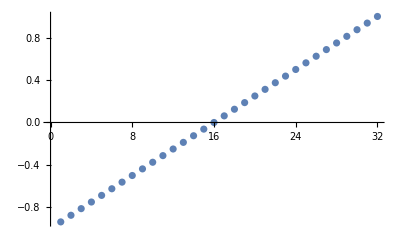

```mathematica
coords={{0.31819805153394598,0.31819805153394681,0},{0.25000660485882059,0.37416132553614562,0},{0.1722075445642903,0.41574578963007908,0},{0.087790644907257506,0.44135337618145382,0},{0,0.45000000000000001,0},{-0.087790644907257742,0.4413533761814537,0},{-0.17220754456429049,0.41574578963007902,0},{-0.2500066048588212,0.37416132553614528,0},{-0.31819805153394659,0.31819805153394609,0},{-0.37416132553614562,0.2500066048588207,0},{-0.41574578963007908,0.1722075445642903,0},{-0.44135337618145359,0.087790644907257923,0},{-0.45000000000000001,0,0}};

Table[ArcTan[coords[[i,1]],coords[[i,2]]],{i,Length[coords]}]
angles={-2.94524,-2.74889,-2.55254,-2.35619,-2.15984,-1.9635,-1.76715,-1.5708,-1.37445,-1.1781,-0.981748,-0.785398,-0.589049,-0.392699,-0.19635,0,0.19635,0.392699,0.589049,0.785398,0.981748,1.1781,1.37445,1.5708,1.76715,1.9635,2.15984,2.35619,2.55254,2.74889,2.94524,3.14159};
Length[angles]
Length[coords]
16angles/Pi
ListPlot[angles/Pi]
```

## Singular function

```mathematica
disp1xy=Sqrt[r]{(kappa-1/2)Cos[theta/2]-1/2 Cos[3theta/2],(kappa+1/2)Sin[theta/2]-1/2Sin[3theta/2]};
disp2xy=Sqrt[r]{(kappa+3/2)Sin[theta/2]+1/2 Sin[3theta/2],-(kappa-3/2)Cos[theta/2]-1/2Cos[3theta/2]};
disp1rt={Cos[theta]disp1xy[[1]]+Sin[theta]disp1xy[[2]],-Sin[theta]disp1xy[[1]]+Cos[theta]disp1xy[[2]]}//FullSimplify;
disp1rt//MatrixForm
disp1rt//CForm
disp2rt={Cos[theta]disp2xy[[1]]+Sin[theta]disp2xy[[2]],-Sin[theta]disp2xy[[1]]+Cos[theta]disp2xy[[2]]}//FullSimplify;
disp2rt//MatrixForm
disp2rt//CForm
graddisp1=Grad[disp1rt,{r,theta},"Polar"]//FullSimplify;
graddisp2=Grad[disp2rt,{r,theta},"Polar"]//FullSimplify;
graddisp1//MatrixForm
graddisp2//MatrixForm
gradvec1={graddisp1[[1,1]],graddisp1[[2,2]],graddisp1[[1,2]]+graddisp1[[2,1]]};
gradvec2={graddisp2[[1,1]],graddisp2[[2,2]],graddisp2[[1,2]]+graddisp2[[2,1]]};
```

(√r Cos[theta/2] (kappa-Cos[theta])
√r (-kappa+Cos[theta]) Sin[theta/2])

(√r (2-kappa+3 Cos[theta]) Sin[theta/2]
-√r Cos[theta/2] (2+kappa-3 Cos[theta]))

((Cos[theta/2] (kappa-Cos[theta]))/(2 √r) | ((2+kappa+Cos[theta]) Sin[theta/2])/(2 √r)
((-kappa+Cos[theta]) Sin[theta/2])/(2 √r) | (Cos[theta/2] (-2+kappa+Cos[theta]))/(2 √r))

(((2-kappa+3 Cos[theta]) Sin[theta/2])/(2 √r) | (Cos[theta/2] (kappa+3 Cos[theta]))/(2 √r)
-(Cos[theta/2] (2+kappa-3 Cos[theta]))/(2 √r) | -((kappa+3 Cos[theta]) Sin[theta/2])/(2 √r))

List(Sqrt(r)*(2 - kappa + 3*Cos(theta))*Sin(theta/2.),
   -(Sqrt(r)*Cos(theta/2.)*(2 + kappa - 3*Cos(theta))))

```mathematica
disp2rt//CForm;
graddisp2[[2]]//CForm
```

List(-0.5*(Cos(theta/2.)*(2 + kappa - 3*Cos(theta)))/Sqrt(r),
   -0.5*((kappa + 3*Cos(theta))*Sin(theta/2.))/Sqrt(r))

```mathematica
disp2rt//CForm
```

List(Sqrt(r)*(2 - kappa + 3*Cos(theta))*Sin(theta/2.),
   -(Sqrt(r)*Cos(theta/2.)*(2 + kappa - 3*Cos(theta))))

```mathematica
Clear[El,nu]
DelastPStress=El/(1-nu^2){{1,nu,0},
{nu,1,0},
{0,0,(1-nu)/2}}//Simplify;
sigmavec=DelastPStress .gradvec1/.kappa->(3-nu)/(1+nu);
sigmatensor={{sigmavec[[1]],sigmavec[[3]]},{sigmavec[[3]],sigmavec[[2]]}};
divsig=Div[sigmatensor,{r,theta},"Polar"]//Simplify
sigmavec=DelastPStress .gradvec2/.kappa->(3-nu)/(1+nu);
sigmatensor={{sigmavec[[1]],sigmavec[[3]]},{sigmavec[[3]],sigmavec[[2]]}};
divsig=Div[sigmatensor,{r,theta},"Polar"]//Simplify
```

{0,0}

{0,0}

```mathematica
DelastPStrain=El (1-nu)/((1+nu)(1-2nu)){
{1,nu/(1-nu),0},{nu/(1-nu),1,0},{0,0,(1-2nu)/(2(1-nu))}}
sigmavec=DelastPStrain .gradvec1/.kappa->(3-4nu);
sigmatensor={{sigmavec[[1]],sigmavec[[3]]},{sigmavec[[3]],sigmavec[[2]]}};
divsig=Div[sigmatensor,{r,theta},"Polar"]//Simplify
sigmavec=DelastPStrain.gradvec2/.kappa->(3-4nu);
sigmatensor={{sigmavec[[1]],sigmavec[[3]]},{sigmavec[[3]],sigmavec[[2]]}};
divsig=Div[sigmatensor,{r,theta},"Polar"]//Simplify
```

{{(El (1-nu))/((1-2 nu) (1+nu)),(El nu)/((1-2 nu) (1+nu)),0},{(El nu)/((1-2 nu) (1+nu)),(El (1-nu))/((1-2 nu) (1+nu)),0},{0,0,El/(2 (1+nu))}}

{0,0}

{0,0}

```mathematica
sigmatensor=1/Sqrt[r]{{Cos[theta/2](1+Sin[theta/2]^2),Cos[theta/2]^2Sin[theta/2]},{Cos[theta/2]^2Sin[theta/2],Cos[theta/2]^3}}
Div[sigmatensor,{r,theta},"Polar"]//Simplify
```

{{(Cos[theta/2] (1+Sin[theta/2]^2))/(√r),(Cos[theta/2]^2 Sin[theta/2])/(√r)},{(Cos[theta/2]^2 Sin[theta/2])/(√r),Cos[theta/2]^3/(√r)}}

{0,0}

```mathematica
rotate={{Cos[theta],Sin[theta]},{-Sin[theta],Cos[theta]}}
disp1xy-Transpose[rotate].disp1rt//Simplify
DelastPStrain=El (1-nu)/((1+nu)(1-2nu)){
{1,nu/(1-nu),0},{nu/(1-nu),1,0},{0,0,(1-2nu)/(2(1-nu))}};
sigmavec=DelastPStrain .gradvec1/.kappa->(3-4nu);
sigmatensorrt={{sigmavec[[1]],sigmavec[[3]]},{sigmavec[[3]],sigmavec[[2]]}};
sigmatensorxy=Transpose[rotate].sigmatensorrt.rotate//Simplify;
sigmatensorxy//MatrixForm
subs={r->Sqrt[x^2+y^2],theta->ArcTan[x,y]};
sigma = sigmatensorxy/.subs//Simplify;
sigma//MatrixForm
Div[sigma,{x,y}]//FullSimplify
```

{{Cos[theta],Sin[theta]},{-Sin[theta],Cos[theta]}}

{0,0}

((El (3 Cos[theta/2]+Cos[(5 theta)/2]))/(4 (1+nu) √r) | (El Cos[theta/2]^2 (-2 Sin[theta/2]+Sin[(3 theta)/2]))/((1+nu) √r)
(El Cos[theta/2]^2 (-2 Sin[theta/2]+Sin[(3 theta)/2]))/((1+nu) √r) | -(El Cos[theta/2]^3 (-3+2 Cos[theta]))/((1+nu) √r))

((El (3 Cos[1/2 ArcTan[x,y]]+Cos[5/2 ArcTan[x,y]]))/(4 (1+nu) (x^2+y^2)^(1/4)) | (El Cos[1/2 ArcTan[x,y]]^2 (-2 Sin[1/2 ArcTan[x,y]]+Sin[3/2 ArcTan[x,y]]))/((1+nu) (x^2+y^2)^(1/4))
(El Cos[1/2 ArcTan[x,y]]^2 (-2 Sin[1/2 ArcTan[x,y]]+Sin[3/2 ArcTan[x,y]]))/((1+nu) (x^2+y^2)^(1/4)) | (El (-2 x+3 √(x^2+y^2)) Cos[1/2 ArcTan[x,y]]^3)/((1+nu) (x^2+y^2)^(3/4)))

{0,0}

```mathematica
pressrt=1/Sqrt[r]Sin[theta/2]
pressrt//CForm;
gradpressrt=Grad[pressrt,{r,theta},"Polar"]
gradpressrt//CForm
rotate//MatrixForm
gradpressxy=Transpose[rotate].gradpressrt/.{r->Sqrt[x^2+y^2],theta->ArcTan[x,y]}//Simplify
laplpressrt =Laplacian[pressrt,{r,theta},"Polar"]
Div[gradpressxy,{x,y}]//FullSimplify
```

Sin[theta/2]/(√r)

{-Sin[theta/2]/(2 r^(3/2)),Cos[theta/2]/(2 r^(3/2))}

(Cos[theta] | Sin[theta]
-Sin[theta] | Cos[theta])

{-(y Cos[1/2 ArcTan[x,y]]+x Sin[1/2 ArcTan[x,y]])/(2 (x^2+y^2)^(5/4)),(x Cos[1/2 ArcTan[x,y]]-y Sin[1/2 ArcTan[x,y]])/(2 (x^2+y^2)^(5/4))}

0

0

List(-0.5*Sin(theta/2.)/Power(r,1.5),Cos(theta/2.)/(2.*Power(r,1.5)))